## Background

For ease of handling all the shape functions are collected in one vector {ψ} . The appropriate shape functions are selected using the Selection matrices when constructing the displacement fields (twist, out - of - plane deflection and bending rotation) over the element i:
θ^i(z,t)={ψ}^T*[A_θ]*{θ}_i
where θ^i(z,t) represents the continuous torsional displacement over the element i, {ψ} is the vector of shape functions, [A_θ] is the selection matrix that selects the right shape functions from the vector of shape functions {ψ}, {θ}_i= {θ_i, θ_(i+1)} is the vector of nodal displacements on element i.

The same is done for   other quantities:
v^i(z,t)={ψ}^T*[A_v]*{v}_i
r^i(z,t)={ψ}^T*[A_r]*{r}_i
V^i(z,t)={ψ}^T*[A_V]*{V}_i
M^i(z,t)={ψ}^T*[A_M]*{M}_i
where v = {v,β} represents the out-of-plane displacement and bending rotation associated with bending, r represents torque per unit length, V represents shear force per unit length, and M represents bending moment per unit length.

### Scaling

Dimensional scaling matrices are required to match the dimensions in the energy expressions for bending. Bending displacement is described by the out-of-plane displacement, v, and bending rotation, β. To arrive at the correct dimensions the bending rotation must be scaled with the length of the beam element:
U^i= 1/2∫_x_i^(x_(i+1)) (EI(∂_x v^i(z,t)))^2 ⅆx=  1/2∫_0^1 EI 1/L_i^4(∂_z ∂_z v^i(z,t))^2 L_i ⅆz = 1/2 1/L_i^3∫_0^1 ({v}_i)^T[S_1][A_v]{ψ}'' EI{ψ}^(''T)[A_v][S_1]{v}_i ⅆz
U^i is the bending strain energy of the element i. When discretizing the nodal displacements must be scaled with the scaling matrix [S_i] to get to the correct dimensions for energy. [S_i]  is of the following form:
[S_1]_i=(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | Li | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | Li)
In the current case the nodal DOFs are organised as follows {ξ}_i={θ_i, v_i, β_i, θ_(i+1), v_(i+1), β_(i+1)}.  β_i, β_(i+1) need to be scaled by L_i, hence the L_i entries at locations [3,3] and [6,6].

NOTE:
> That matrices [A_v], [S_1] are symmetric, hence no Transpose is required.
> when changing the derivatives from physical coordinate x to non-dimensional coordinate z= (x-x_i)/L_i, the derivates scale as:
∂_x () = ∂_z ()*∂_x z= 1/L_i∂_z ()
∂_xx () = ∂_z (∂_z ()*∂_x z)∂_x z= 1/L_i∂_z (1/L_i∂_z ()) =1/L_i^2∂_zz () 
> Matrix [S_1] is element dependent (on the length of the element)
> Matrix [A_v] is element independent.

### Derivation of the Elemental matrices

The main part of the FEM model are elemental mass and stiffness matrices, and the matrices for generalised forces. The elemental matrices are derived in three steps: 
1) derive the nucleus of the elemental matrix (numerical coefficients which are equal for all the elements based on the selection of the shape functions):

U^i= 1/2 1/L_i^3∫_0^1 ({v}_i)^T[S_1][A_v]{ψ}'' EI{ψ}^(''T)[A_v][S_1]{v}_i ⅆz = 1/2 1/L_i^3({v}_i)^T[S_1][∫_0^1 [A_v]{ψ}'' EI{ψ}^(''T)[A_v]ⅆz ][S_1]{v}_i =1/2 EI/L_i^3({v}_i)^T[S_1][N_KB ][S_1]{v}_i 
N_KB=[∫_0^1 [A_v]{ψ}''{ψ}^(''T)[A_v]ⅆz ]

where N_KB is the nucleus of the stiffness matrix due to bending.  

2) scale the nucleus with the physical properties and the scaling matrix of every individual element to get the elemental stiffness matrix due to bending:
K_B^i = ((EI_i/L_i^3[S_1])_i[N_KB ][S_1])_i
> note, that 1/2 is dropped since the stiffness matrix is obtained as a derivative of the strain energy wrt. the displacement DOFs.

3) Add together the different contributions to the complete stiffness matrix:
K_i= K_T^i+K_TB^i+K_BT^i+K_B^i

The same process is repeated for the elemental mass matrix and the matrices governing the distribution of generalised forces (external forces.)

## Beam Properties

### Beam properties

```mathematica
(*Number of elements in the beam (max 5)*)
n = 3;

(*Lengths of individual beam elements [m]*)
L = {L1, L2, L3, L4, L5}; 
(*specific mass [kg/m]*)
M = {m1, m2, m3, m4, m5};
(*specific mass polar moment of inertia [kgm^2/m]*)
Ip={ρIp1, ρIp2, ρIp3, ρIp4, ρIp5};
(*offset of the cross-sectional mass matrix [m]*)
d = {d1, d2, d3, d4, d5};
(*Torsinal stiffness [Nm^2]*)
GJ = {GJ1, GJ2, GJ3, GJ4, GJ5};
(*Bending stiffness [Nm^2]*)
EI = {EI1, EI2, EI3, EI4, EI5};
(*Bend-twist coupling [Nm^2]*)
KBT = {K1, K2, K3, K4, K5};
```

### Shape functions

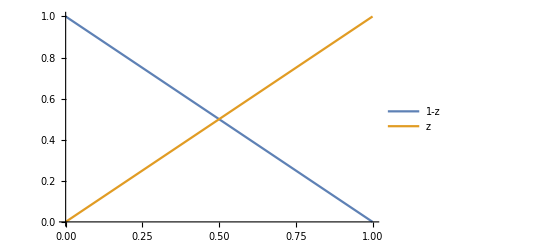

```mathematica
(*Torison*)
shapeT = {1-z, z};
shapeT1 = D[shapeT, {z,1}];

Plot[shapeT, {z,0,1}, PlotLegends->"Expressions"]
```

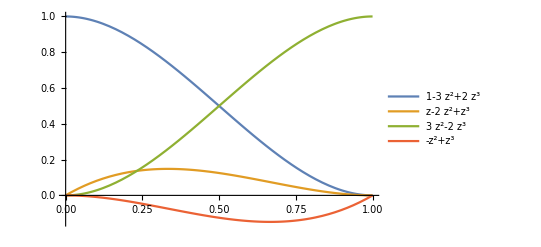

```mathematica
(*Bending*)
shapeB = {2*z^3-3*z^2+1, z^3-2*z^2+z, 3*z^2-2*z^3, z^3-z^2};
shapeB1 = D[shapeB, {z,1}];
shapeB2 = D[shapeB, {z,2}];

Plot[shapeB, {z,0,1}, PlotLegends->"Expressions"]
```

```mathematica
(*Combined shape functions:*)
psi = {shapeT[[1]], shapeB[[1]], shapeB[[2]], shapeT[[2]], shapeB[[3]], shapeB[[4]]};
psi1 = D[psi, {z,1}];
psi2 = D[psi, {z,2}];

(*Selection matricies:*)
(*Torsion DOFs*)
ATh = ConstantArray[0,{6,6}];
ATh[[1,1]] = 1; ATh[[4,4]]=1;

(*Bending DOFs*)
Av = ConstantArray[0,{6,6}];
Av[[2,2]] = 1; Av[[3,3]]=1;Av[[5,5]] = 1; Av[[6,6]]=1;

(*Torque*)
ATR = ConstantArray[0,{6,6}];
ATR[[1,1]] = 1; ATR[[4,4]]=1;

(*Shear force*)
ABV = ConstantArray[0,{6,6}];
ABV[[1,2]] = 1; ABV[[4,5]]=1;

(*Bending moment*)
ABM = ConstantArray[0,{6,6}];
ABM[[1,3]] = 1; ABM[[4,6]]=1;

ATh//MatrixForm
Av//MatrixForm
ATR//MatrixForm
ABV //MatrixForm
ABM //MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

### Dimensional Scaling Matrices

```mathematica
(*Dimensional scaling required to match dimensions of the v and beta DOFs*)
S1 = Table[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0, L[[i]],0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0, L[[i]]}}, {i,n}];
S2 = Table[{{1/L[[i]],0,0,0,0,0},{0,1/L[[i]],0,0,0,0},{0,0, 1,0,0,0},{0,0,0,1/L[[i]],0,0},{0,0,0,0,1/L[[i]],0},{0,0,0,0,0, 1}}, {i,n}];

S1[[1]]//MatrixForm
S2[[1]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | L1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | L1)

(1/L1 | 0 | 0 | 0 | 0 | 0
0 | 1/L1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1/L1 | 0 | 0
0 | 0 | 0 | 0 | 1/L1 | 0
0 | 0 | 0 | 0 | 0 | 1)

## Stiffness Matrix [KK]

```mathematica
(*Torsion*)
nucleusKGJ = ∫_0^1 Outer[Times, ATh.psi1, psi1.ATh]ⅆz;
(*Twist-bend coupling*)
nucleusKK1 = ∫_0^1 Outer[Times, ATh.psi1, psi2.Av]ⅆz;
(*Bend-twist coupling*)
nucleusKK2 = ∫_0^1 Outer[Times, Av.psi2, psi1.ATh]ⅆz;
(*Bending*)
nucleusKEI = ∫_0^1 Outer[Times, Av.psi2, psi2.Av]ⅆz;

nucleusKGJ//MatrixForm
nucleusKK1//MatrixForm
nucleusKK2//MatrixForm
nucleusKEI//MatrixForm
```

(1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 12 | 6 | 0 | -12 | 6
0 | 6 | 4 | 0 | -6 | 2
0 | 0 | 0 | 0 | 0 | 0
0 | -12 | -6 | 0 | 12 | -6
0 | 6 | 2 | 0 | -6 | 4)

```mathematica
(*Element stiffness matrix:*)
KKElem = Table[
(GJ[[i]]/L[[i]])*Transpose[S1[[i]]]. nucleusKGJ.S1[[i]]+
(KBT[[i]]/L[[i]]^2)*Transpose[S1[[i]]]. nucleusKK1.S1[[i]]+
(KBT[[i]]/L[[i]]^2)*Transpose[S1[[i]]]. nucleusKK2.S1[[i]]+
(EI[[i]]/L[[i]]^3)*Transpose[S1[[i]]]. nucleusKEI.S1[[i]],
{i,n}];

KKElem[[1]]//MatrixForm
```

(GJ1/L1 | 0 | K1/L1 | -GJ1/L1 | 0 | -K1/L1
0 | (12 EI1)/L1^3 | (6 EI1)/L1^2 | 0 | -(12 EI1)/L1^3 | (6 EI1)/L1^2
K1/L1 | (6 EI1)/L1^2 | (4 EI1)/L1 | -K1/L1 | -(6 EI1)/L1^2 | (2 EI1)/L1
-GJ1/L1 | 0 | -K1/L1 | GJ1/L1 | 0 | K1/L1
0 | -(12 EI1)/L1^3 | -(6 EI1)/L1^2 | 0 | (12 EI1)/L1^3 | -(6 EI1)/L1^2
-K1/L1 | (6 EI1)/L1^2 | (2 EI1)/L1 | K1/L1 | -(6 EI1)/L1^2 | (4 EI1)/L1)

```mathematica
(*Global stiffness matrix:*)
KK = ConstantArray[0,{3*(n+1), 3*(n+1)}];
Do[KK[[3*i-2;;3*i+3,3*i-2;;3*i+3]] =  KK[[3*i-2;;3*i+3,3*i-2;;3*i+3]]+KKElem[[i]] ,{i,n}];
KK//MatrixForm
```

(GJ1/L1 | 0 | K1/L1 | -GJ1/L1 | 0 | -K1/L1 | 0 | 0 | 0 | 0 | 0 | 0
0 | (12 EI1)/L1^3 | (6 EI1)/L1^2 | 0 | -(12 EI1)/L1^3 | (6 EI1)/L1^2 | 0 | 0 | 0 | 0 | 0 | 0
K1/L1 | (6 EI1)/L1^2 | (4 EI1)/L1 | -K1/L1 | -(6 EI1)/L1^2 | (2 EI1)/L1 | 0 | 0 | 0 | 0 | 0 | 0
-GJ1/L1 | 0 | -K1/L1 | GJ1/L1+GJ2/L2 | 0 | K1/L1+K2/L2 | -GJ2/L2 | 0 | -K2/L2 | 0 | 0 | 0
0 | -(12 EI1)/L1^3 | -(6 EI1)/L1^2 | 0 | (12 EI1)/L1^3+(12 EI2)/L2^3 | -(6 EI1)/L1^2+(6 EI2)/L2^2 | 0 | -(12 EI2)/L2^3 | (6 EI2)/L2^2 | 0 | 0 | 0
-K1/L1 | (6 EI1)/L1^2 | (2 EI1)/L1 | K1/L1+K2/L2 | -(6 EI1)/L1^2+(6 EI2)/L2^2 | (4 EI1)/L1+(4 EI2)/L2 | -K2/L2 | -(6 EI2)/L2^2 | (2 EI2)/L2 | 0 | 0 | 0
0 | 0 | 0 | -GJ2/L2 | 0 | -K2/L2 | GJ2/L2+GJ3/L3 | 0 | K2/L2+K3/L3 | -GJ3/L3 | 0 | -K3/L3
0 | 0 | 0 | 0 | -(12 EI2)/L2^3 | -(6 EI2)/L2^2 | 0 | (12 EI2)/L2^3+(12 EI3)/L3^3 | -(6 EI2)/L2^2+(6 EI3)/L3^2 | 0 | -(12 EI3)/L3^3 | (6 EI3)/L3^2
0 | 0 | 0 | -K2/L2 | (6 EI2)/L2^2 | (2 EI2)/L2 | K2/L2+K3/L3 | -(6 EI2)/L2^2+(6 EI3)/L3^2 | (4 EI2)/L2+(4 EI3)/L3 | -K3/L3 | -(6 EI3)/L3^2 | (2 EI3)/L3
0 | 0 | 0 | 0 | 0 | 0 | -GJ3/L3 | 0 | -K3/L3 | GJ3/L3 | 0 | K3/L3
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(12 EI3)/L3^3 | -(6 EI3)/L3^2 | 0 | (12 EI3)/L3^3 | -(6 EI3)/L3^2
0 | 0 | 0 | 0 | 0 | 0 | -K3/L3 | (6 EI3)/L3^2 | (2 EI3)/L3 | K3/L3 | -(6 EI3)/L3^2 | (4 EI3)/L3)

## Mass Matrix [MM]

```mathematica
(*Torsion*)
nucleusMTT = ∫_0^1 Outer[Times, ATh.psi, psi.ATh]ⅆz;
(*Twist-bend coupling*)
nucleusMTB = ∫_0^1 Outer[Times, ATh.psi, psi.Av]ⅆz;
(*Bend-twist coupling*)
nucleusMBT = ∫_0^1 Outer[Times, Av.psi, psi.ATh]ⅆz;
(*Bending*)
nucleusMBB = ∫_0^1 Outer[Times, Av.psi, psi.Av]ⅆz;

nucleusMTT//MatrixForm
nucleusMTB//MatrixForm
nucleusMBT//MatrixForm
nucleusMBB//MatrixForm
```

(1/3 | 0 | 0 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 0 | 1/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 7/20 | 1/20 | 0 | 3/20 | -1/30
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 3/20 | 1/30 | 0 | 7/20 | -1/20
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
7/20 | 0 | 0 | 3/20 | 0 | 0
1/20 | 0 | 0 | 1/30 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
3/20 | 0 | 0 | 7/20 | 0 | 0
-1/30 | 0 | 0 | -1/20 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 13/35 | 11/210 | 0 | 9/70 | -13/420
0 | 11/210 | 1/105 | 0 | 13/420 | -1/140
0 | 0 | 0 | 0 | 0 | 0
0 | 9/70 | 13/420 | 0 | 13/35 | -11/210
0 | -13/420 | -1/140 | 0 | -11/210 | 1/105)

```mathematica
(*Element mass matrix:*)
MMElem = Table[
(Ip[[i]]*L[[i]])*Transpose[S1[[i]]]. nucleusMTT.S1[[i]]+
(M[[i]]*d[[i]]*L[[i]])*Transpose[S1[[i]]]. nucleusMTB.S1[[i]]+
(M[[i]]*d[[i]]*L[[i]])*Transpose[S1[[i]]]. nucleusMBT.S1[[i]]+
(M[[i]]*L[[i]])*Transpose[S1[[i]]]. nucleusMBB.S1[[i]],
{i,n}];

MMElem[[1]]//MatrixForm
```

((L1 ρIp1)/3 | (7 d1 L1 m1)/20 | 1/20 d1 L1^2 m1 | (L1 ρIp1)/6 | (3 d1 L1 m1)/20 | -1/30 d1 L1^2 m1
(7 d1 L1 m1)/20 | (13 L1 m1)/35 | (11 L1^2 m1)/210 | (3 d1 L1 m1)/20 | (9 L1 m1)/70 | -(13 L1^2 m1)/420
1/20 d1 L1^2 m1 | (11 L1^2 m1)/210 | (L1^3 m1)/105 | 1/30 d1 L1^2 m1 | (13 L1^2 m1)/420 | -(L1^3 m1)/140
(L1 ρIp1)/6 | (3 d1 L1 m1)/20 | 1/30 d1 L1^2 m1 | (L1 ρIp1)/3 | (7 d1 L1 m1)/20 | -1/20 d1 L1^2 m1
(3 d1 L1 m1)/20 | (9 L1 m1)/70 | (13 L1^2 m1)/420 | (7 d1 L1 m1)/20 | (13 L1 m1)/35 | -(11 L1^2 m1)/210
-1/30 d1 L1^2 m1 | -(13 L1^2 m1)/420 | -(L1^3 m1)/140 | -1/20 d1 L1^2 m1 | -(11 L1^2 m1)/210 | (L1^3 m1)/105)

```mathematica
(*Global mass matrix:*)
MM = ConstantArray[0,{3*(n+1), 3*(n+1)}];
Do[MM[[3*i-2;;3*i+3,3*i-2;;3*i+3]] =  MM[[3*i-2;;3*i+3,3*i-2;;3*i+3]]+MMElem[[i]] ,{i,n}];
MM//MatrixForm
```

((L1 ρIp1)/3 | (7 d1 L1 m1)/20 | 1/20 d1 L1^2 m1 | (L1 ρIp1)/6 | (3 d1 L1 m1)/20 | -1/30 d1 L1^2 m1 | 0 | 0 | 0 | 0 | 0 | 0
(7 d1 L1 m1)/20 | (13 L1 m1)/35 | (11 L1^2 m1)/210 | (3 d1 L1 m1)/20 | (9 L1 m1)/70 | -(13 L1^2 m1)/420 | 0 | 0 | 0 | 0 | 0 | 0
1/20 d1 L1^2 m1 | (11 L1^2 m1)/210 | (L1^3 m1)/105 | 1/30 d1 L1^2 m1 | (13 L1^2 m1)/420 | -(L1^3 m1)/140 | 0 | 0 | 0 | 0 | 0 | 0
(L1 ρIp1)/6 | (3 d1 L1 m1)/20 | 1/30 d1 L1^2 m1 | (L1 ρIp1)/3+(L2 ρIp2)/3 | (7 d1 L1 m1)/20+(7 d2 L2 m2)/20 | -1/20 d1 L1^2 m1+1/20 d2 L2^2 m2 | (L2 ρIp2)/6 | (3 d2 L2 m2)/20 | -1/30 d2 L2^2 m2 | 0 | 0 | 0
(3 d1 L1 m1)/20 | (9 L1 m1)/70 | (13 L1^2 m1)/420 | (7 d1 L1 m1)/20+(7 d2 L2 m2)/20 | (13 L1 m1)/35+(13 L2 m2)/35 | -(11 L1^2 m1)/210+(11 L2^2 m2)/210 | (3 d2 L2 m2)/20 | (9 L2 m2)/70 | -(13 L2^2 m2)/420 | 0 | 0 | 0
-1/30 d1 L1^2 m1 | -(13 L1^2 m1)/420 | -(L1^3 m1)/140 | -1/20 d1 L1^2 m1+1/20 d2 L2^2 m2 | -(11 L1^2 m1)/210+(11 L2^2 m2)/210 | (L1^3 m1)/105+(L2^3 m2)/105 | 1/30 d2 L2^2 m2 | (13 L2^2 m2)/420 | -(L2^3 m2)/140 | 0 | 0 | 0
0 | 0 | 0 | (L2 ρIp2)/6 | (3 d2 L2 m2)/20 | 1/30 d2 L2^2 m2 | (L2 ρIp2)/3+(L3 ρIp3)/3 | (7 d2 L2 m2)/20+(7 d3 L3 m3)/20 | -1/20 d2 L2^2 m2+1/20 d3 L3^2 m3 | (L3 ρIp3)/6 | (3 d3 L3 m3)/20 | -1/30 d3 L3^2 m3
0 | 0 | 0 | (3 d2 L2 m2)/20 | (9 L2 m2)/70 | (13 L2^2 m2)/420 | (7 d2 L2 m2)/20+(7 d3 L3 m3)/20 | (13 L2 m2)/35+(13 L3 m3)/35 | -(11 L2^2 m2)/210+(11 L3^2 m3)/210 | (3 d3 L3 m3)/20 | (9 L3 m3)/70 | -(13 L3^2 m3)/420
0 | 0 | 0 | -1/30 d2 L2^2 m2 | -(13 L2^2 m2)/420 | -(L2^3 m2)/140 | -1/20 d2 L2^2 m2+1/20 d3 L3^2 m3 | -(11 L2^2 m2)/210+(11 L3^2 m3)/210 | (L2^3 m2)/105+(L3^3 m3)/105 | 1/30 d3 L3^2 m3 | (13 L3^2 m3)/420 | -(L3^3 m3)/140
0 | 0 | 0 | 0 | 0 | 0 | (L3 ρIp3)/6 | (3 d3 L3 m3)/20 | 1/30 d3 L3^2 m3 | (L3 ρIp3)/3 | (7 d3 L3 m3)/20 | -1/20 d3 L3^2 m3
0 | 0 | 0 | 0 | 0 | 0 | (3 d3 L3 m3)/20 | (9 L3 m3)/70 | (13 L3^2 m3)/420 | (7 d3 L3 m3)/20 | (13 L3 m3)/35 | -(11 L3^2 m3)/210
0 | 0 | 0 | 0 | 0 | 0 | -1/30 d3 L3^2 m3 | -(13 L3^2 m3)/420 | -(L3^3 m3)/140 | -1/20 d3 L3^2 m3 | -(11 L3^2 m3)/210 | (L3^3 m3)/105)

## Aerodynamic Mass Matrix [MMae]

```mathematica
(*F = BB.y_ddot is the applied aerodynamic load due to structural deformations
F = {r, f, q} ... aerodynamic torque, shear force, bending moment, respectively, all per unit length, due to acceleration of DOFs
y= {θ, v, β} ... torsional twist, out-of-plane-deflection, derivative of the out-of-plane dflection in spanwise diection (dv/dx), respectively

note: 
> q = 0 since aerodynamic forces do not induce pure bending moment
> aerodynmic forces do not depend on β.

Hence FF has zero last row and column.
*)
(*matrix of aerodynamic loads due to structural displacement*)
BBaero = ConstantArray[0,{3,3}];
BBaero[[1,1]]= B11;
BBaero[[1,2]] = B12;
BBaero[[2,1]] = B21;
BBaero[[2,2]] = B22;

(*Selection matrix*)
AAE = ConstantArray[0,{3,6}];
AAE[[1,1]] = psi[[1]]; AAE[[1,4]] = psi[[4]];
AAE[[2,2]] = psi[[2]]; AAE[[2,3]] = psi[[3]];AAE[[2,5]] = psi[[5]]; AAE[[2,6]] = psi[[6]];
AAE[[3,2]] = psi1[[2]]; AAE[[3,3]] = psi1[[3]];AAE[[3,5]] = psi1[[5]]; AAE[[3,6]] = psi[[6]];

(*Aerodynamic stiffness matrix*)
nucleusBB = ∫_0^1 Transpose[AAE].BBaero.AAEⅆz;
BBaero//MatrixForm
AAE//MatrixForm
nucleusBB//MatrixForm
```

(B11 | B12 | 0
B21 | B22 | 0
0 | 0 | 0)

(1-z | 0 | 0 | z | 0 | 0
0 | 1-3 z^2+2 z^3 | z-2 z^2+z^3 | 0 | 3 z^2-2 z^3 | -z^2+z^3
0 | -6 z+6 z^2 | 1-4 z+3 z^2 | 0 | 6 z-6 z^2 | -z^2+z^3)

(B11/3 | (7 B12)/20 | B12/20 | B11/6 | (3 B12)/20 | -B12/30
(7 B21)/20 | (13 B22)/35 | (11 B22)/210 | (3 B21)/20 | (9 B22)/70 | -(13 B22)/420
B21/20 | (11 B22)/210 | B22/105 | B21/30 | (13 B22)/420 | -B22/140
B11/6 | (3 B12)/20 | B12/30 | B11/3 | (7 B12)/20 | -B12/20
(3 B21)/20 | (9 B22)/70 | (13 B22)/420 | (7 B21)/20 | (13 B22)/35 | -(11 B22)/210
-B21/30 | -(13 B22)/420 | -B22/140 | -B21/20 | -(11 B22)/210 | B22/105)

```mathematica
(*Element matrix for virtual work:*)
BBElem = Table[L[[i]]*Transpose[S1[[i]]]. nucleusBB.S1[[i]],{i,n}];
BBElem[[1]]//MatrixForm
```

((B11 L1)/3 | (7 B12 L1)/20 | (B12 L1^2)/20 | (B11 L1)/6 | (3 B12 L1)/20 | -(B12 L1^2)/30
(7 B21 L1)/20 | (13 B22 L1)/35 | (11 B22 L1^2)/210 | (3 B21 L1)/20 | (9 B22 L1)/70 | -(13 B22 L1^2)/420
(B21 L1^2)/20 | (11 B22 L1^2)/210 | (B22 L1^3)/105 | (B21 L1^2)/30 | (13 B22 L1^2)/420 | -(B22 L1^3)/140
(B11 L1)/6 | (3 B12 L1)/20 | (B12 L1^2)/30 | (B11 L1)/3 | (7 B12 L1)/20 | -(B12 L1^2)/20
(3 B21 L1)/20 | (9 B22 L1)/70 | (13 B22 L1^2)/420 | (7 B21 L1)/20 | (13 B22 L1)/35 | -(11 B22 L1^2)/210
-(B21 L1^2)/30 | -(13 B22 L1^2)/420 | -(B22 L1^3)/140 | -(B21 L1^2)/20 | -(11 B22 L1^2)/210 | (B22 L1^3)/105)

```mathematica
(*Global aerodynamic mass matrix:*)
BB = ConstantArray[0,{3*(n+1), 3*(n+1)}];
Do[BB[[3*i-2;;3*i+3,3*i-2;;3*i+3]] =  BB[[3*i-2;;3*i+3,3*i-2;;3*i+3]]+BBElem[[i]] ,{i,n}];
BB//MatrixForm
```

((B11 L1)/3 | (7 B12 L1)/20 | (B12 L1^2)/20 | (B11 L1)/6 | (3 B12 L1)/20 | -(B12 L1^2)/30 | 0 | 0 | 0 | 0 | 0 | 0
(7 B21 L1)/20 | (13 B22 L1)/35 | (11 B22 L1^2)/210 | (3 B21 L1)/20 | (9 B22 L1)/70 | -(13 B22 L1^2)/420 | 0 | 0 | 0 | 0 | 0 | 0
(B21 L1^2)/20 | (11 B22 L1^2)/210 | (B22 L1^3)/105 | (B21 L1^2)/30 | (13 B22 L1^2)/420 | -(B22 L1^3)/140 | 0 | 0 | 0 | 0 | 0 | 0
(B11 L1)/6 | (3 B12 L1)/20 | (B12 L1^2)/30 | (B11 L1)/3+(B11 L2)/3 | (7 B12 L1)/20+(7 B12 L2)/20 | -(B12 L1^2)/20+(B12 L2^2)/20 | (B11 L2)/6 | (3 B12 L2)/20 | -(B12 L2^2)/30 | 0 | 0 | 0
(3 B21 L1)/20 | (9 B22 L1)/70 | (13 B22 L1^2)/420 | (7 B21 L1)/20+(7 B21 L2)/20 | (13 B22 L1)/35+(13 B22 L2)/35 | -(11 B22 L1^2)/210+(11 B22 L2^2)/210 | (3 B21 L2)/20 | (9 B22 L2)/70 | -(13 B22 L2^2)/420 | 0 | 0 | 0
-(B21 L1^2)/30 | -(13 B22 L1^2)/420 | -(B22 L1^3)/140 | -(B21 L1^2)/20+(B21 L2^2)/20 | -(11 B22 L1^2)/210+(11 B22 L2^2)/210 | (B22 L1^3)/105+(B22 L2^3)/105 | (B21 L2^2)/30 | (13 B22 L2^2)/420 | -(B22 L2^3)/140 | 0 | 0 | 0
0 | 0 | 0 | (B11 L2)/6 | (3 B12 L2)/20 | (B12 L2^2)/30 | (B11 L2)/3+(B11 L3)/3 | (7 B12 L2)/20+(7 B12 L3)/20 | -(B12 L2^2)/20+(B12 L3^2)/20 | (B11 L3)/6 | (3 B12 L3)/20 | -(B12 L3^2)/30
0 | 0 | 0 | (3 B21 L2)/20 | (9 B22 L2)/70 | (13 B22 L2^2)/420 | (7 B21 L2)/20+(7 B21 L3)/20 | (13 B22 L2)/35+(13 B22 L3)/35 | -(11 B22 L2^2)/210+(11 B22 L3^2)/210 | (3 B21 L3)/20 | (9 B22 L3)/70 | -(13 B22 L3^2)/420
0 | 0 | 0 | -(B21 L2^2)/30 | -(13 B22 L2^2)/420 | -(B22 L2^3)/140 | -(B21 L2^2)/20+(B21 L3^2)/20 | -(11 B22 L2^2)/210+(11 B22 L3^2)/210 | (B22 L2^3)/105+(B22 L3^3)/105 | (B21 L3^2)/30 | (13 B22 L3^2)/420 | -(B22 L3^3)/140
0 | 0 | 0 | 0 | 0 | 0 | (B11 L3)/6 | (3 B12 L3)/20 | (B12 L3^2)/30 | (B11 L3)/3 | (7 B12 L3)/20 | -(B12 L3^2)/20
0 | 0 | 0 | 0 | 0 | 0 | (3 B21 L3)/20 | (9 B22 L3)/70 | (13 B22 L3^2)/420 | (7 B21 L3)/20 | (13 B22 L3)/35 | -(11 B22 L3^2)/210
0 | 0 | 0 | 0 | 0 | 0 | -(B21 L3^2)/30 | -(13 B22 L3^2)/420 | -(B22 L3^3)/140 | -(B21 L3^2)/20 | -(11 B22 L3^2)/210 | (B22 L3^3)/105)

## Aerodynamic Damping Matrix [CCae]

```mathematica
(*F = DD.y_dot is the applied aerodynamic load due to the rate of structural deformations
F = {r, f, q} ... aerodynamic torque, shear force, bending moment, respectively, all per unit length, due to rate of DOFs
y= {θ, v, β} ... torsional twist, out-of-plane-deflection, derivative of the out-of-plane dflection in spanwise diection (dv/dx), respectively

note: 
> q = 0 since aerodynamic forces do not induce pure bending moment
> aerodynmic forces do not depend on β.

Hence FF has zero last row and column.
*)
(*matrix of aerodynamic loads due to structural displacement*)
DDaero = ConstantArray[0,{3,3}];
DDaero[[1,1]]= D11;
DDaero[[1,2]] = D12;
DDaero[[2,1]] = D21;
DDaero[[2,2]] = D22;

(*Selection matrix*)
AAE = ConstantArray[0,{3,6}];
AAE[[1,1]] = psi[[1]]; AAE[[1,4]] = psi[[4]];
AAE[[2,2]] = psi[[2]]; AAE[[2,3]] = psi[[3]];AAE[[2,5]] = psi[[5]]; AAE[[2,6]] = psi[[6]];
AAE[[3,2]] = psi1[[2]]; AAE[[3,3]] = psi1[[3]];AAE[[3,5]] = psi1[[5]]; AAE[[3,6]] = psi[[6]];

(*Aerodynamic stiffness matrix*)
nucleusDD = ∫_0^1 Transpose[AAE].DDaero.AAEⅆz;
DDaero//MatrixForm
AAE//MatrixForm
nucleusDD//MatrixForm
```

(D11 | D12 | 0
D21 | D22 | 0
0 | 0 | 0)

(1-z | 0 | 0 | z | 0 | 0
0 | 1-3 z^2+2 z^3 | z-2 z^2+z^3 | 0 | 3 z^2-2 z^3 | -z^2+z^3
0 | -6 z+6 z^2 | 1-4 z+3 z^2 | 0 | 6 z-6 z^2 | -z^2+z^3)

(D11/3 | (7 D12)/20 | D12/20 | D11/6 | (3 D12)/20 | -D12/30
(7 D21)/20 | (13 D22)/35 | (11 D22)/210 | (3 D21)/20 | (9 D22)/70 | -(13 D22)/420
D21/20 | (11 D22)/210 | D22/105 | D21/30 | (13 D22)/420 | -D22/140
D11/6 | (3 D12)/20 | D12/30 | D11/3 | (7 D12)/20 | -D12/20
(3 D21)/20 | (9 D22)/70 | (13 D22)/420 | (7 D21)/20 | (13 D22)/35 | -(11 D22)/210
-D21/30 | -(13 D22)/420 | -D22/140 | -D21/20 | -(11 D22)/210 | D22/105)

```mathematica
(*Element matrix for virtual work:*)
DDElem = Table[L[[i]]*Transpose[S1[[i]]]. nucleusDD.S1[[i]],{i,n}];
DDElem[[1]]//MatrixForm
```

((D11 L1)/3 | (7 D12 L1)/20 | (D12 L1^2)/20 | (D11 L1)/6 | (3 D12 L1)/20 | -(D12 L1^2)/30
(7 D21 L1)/20 | (13 D22 L1)/35 | (11 D22 L1^2)/210 | (3 D21 L1)/20 | (9 D22 L1)/70 | -(13 D22 L1^2)/420
(D21 L1^2)/20 | (11 D22 L1^2)/210 | (D22 L1^3)/105 | (D21 L1^2)/30 | (13 D22 L1^2)/420 | -(D22 L1^3)/140
(D11 L1)/6 | (3 D12 L1)/20 | (D12 L1^2)/30 | (D11 L1)/3 | (7 D12 L1)/20 | -(D12 L1^2)/20
(3 D21 L1)/20 | (9 D22 L1)/70 | (13 D22 L1^2)/420 | (7 D21 L1)/20 | (13 D22 L1)/35 | -(11 D22 L1^2)/210
-(D21 L1^2)/30 | -(13 D22 L1^2)/420 | -(D22 L1^3)/140 | -(D21 L1^2)/20 | -(11 D22 L1^2)/210 | (D22 L1^3)/105)

```mathematica
(*Global aerodynamic mass matrix:*)
DD = ConstantArray[0,{3*(n+1), 3*(n+1)}];
Do[DD[[3*i-2;;3*i+3,3*i-2;;3*i+3]] =  DD[[3*i-2;;3*i+3,3*i-2;;3*i+3]]+DDElem[[i]] ,{i,n}];
DD//MatrixForm
```

((D11 L1)/3 | (7 D12 L1)/20 | (D12 L1^2)/20 | (D11 L1)/6 | (3 D12 L1)/20 | -(D12 L1^2)/30 | 0 | 0 | 0 | 0 | 0 | 0
(7 D21 L1)/20 | (13 D22 L1)/35 | (11 D22 L1^2)/210 | (3 D21 L1)/20 | (9 D22 L1)/70 | -(13 D22 L1^2)/420 | 0 | 0 | 0 | 0 | 0 | 0
(D21 L1^2)/20 | (11 D22 L1^2)/210 | (D22 L1^3)/105 | (D21 L1^2)/30 | (13 D22 L1^2)/420 | -(D22 L1^3)/140 | 0 | 0 | 0 | 0 | 0 | 0
(D11 L1)/6 | (3 D12 L1)/20 | (D12 L1^2)/30 | (D11 L1)/3+(D11 L2)/3 | (7 D12 L1)/20+(7 D12 L2)/20 | -(D12 L1^2)/20+(D12 L2^2)/20 | (D11 L2)/6 | (3 D12 L2)/20 | -(D12 L2^2)/30 | 0 | 0 | 0
(3 D21 L1)/20 | (9 D22 L1)/70 | (13 D22 L1^2)/420 | (7 D21 L1)/20+(7 D21 L2)/20 | (13 D22 L1)/35+(13 D22 L2)/35 | -(11 D22 L1^2)/210+(11 D22 L2^2)/210 | (3 D21 L2)/20 | (9 D22 L2)/70 | -(13 D22 L2^2)/420 | 0 | 0 | 0
-(D21 L1^2)/30 | -(13 D22 L1^2)/420 | -(D22 L1^3)/140 | -(D21 L1^2)/20+(D21 L2^2)/20 | -(11 D22 L1^2)/210+(11 D22 L2^2)/210 | (D22 L1^3)/105+(D22 L2^3)/105 | (D21 L2^2)/30 | (13 D22 L2^2)/420 | -(D22 L2^3)/140 | 0 | 0 | 0
0 | 0 | 0 | (D11 L2)/6 | (3 D12 L2)/20 | (D12 L2^2)/30 | (D11 L2)/3+(D11 L3)/3 | (7 D12 L2)/20+(7 D12 L3)/20 | -(D12 L2^2)/20+(D12 L3^2)/20 | (D11 L3)/6 | (3 D12 L3)/20 | -(D12 L3^2)/30
0 | 0 | 0 | (3 D21 L2)/20 | (9 D22 L2)/70 | (13 D22 L2^2)/420 | (7 D21 L2)/20+(7 D21 L3)/20 | (13 D22 L2)/35+(13 D22 L3)/35 | -(11 D22 L2^2)/210+(11 D22 L3^2)/210 | (3 D21 L3)/20 | (9 D22 L3)/70 | -(13 D22 L3^2)/420
0 | 0 | 0 | -(D21 L2^2)/30 | -(13 D22 L2^2)/420 | -(D22 L2^3)/140 | -(D21 L2^2)/20+(D21 L3^2)/20 | -(11 D22 L2^2)/210+(11 D22 L3^2)/210 | (D22 L2^3)/105+(D22 L3^3)/105 | (D21 L3^2)/30 | (13 D22 L3^2)/420 | -(D22 L3^3)/140
0 | 0 | 0 | 0 | 0 | 0 | (D11 L3)/6 | (3 D12 L3)/20 | (D12 L3^2)/30 | (D11 L3)/3 | (7 D12 L3)/20 | -(D12 L3^2)/20
0 | 0 | 0 | 0 | 0 | 0 | (3 D21 L3)/20 | (9 D22 L3)/70 | (13 D22 L3^2)/420 | (7 D21 L3)/20 | (13 D22 L3)/35 | -(11 D22 L3^2)/210
0 | 0 | 0 | 0 | 0 | 0 | -(D21 L3^2)/30 | -(13 D22 L3^2)/420 | -(D22 L3^3)/140 | -(D21 L3^2)/20 | -(11 D22 L3^2)/210 | (D22 L3^3)/105)

## Aerodynamic Stiffness Matrix [KKae]

```mathematica
(*F = FF.y is the applied aerodynamic load due to structural deformations
F = {r, f, q} ... aerodynamic torque, shear force, bending moment, respectively, all per unit length
y= {θ, v, β} ... torsional twist, out-of-plane-deflection, derivative of the out-of-plane dflection in spanwise diection (dv/dx), respectively

note: 
> q = 0 since aerodynamic forces do not induce pure bending moment
> aerodynmic forces do not depend on β.

Hence FF has zero last row and column.
*)
(*matrix of aerodynamic loads due to structural displacement*)
FFaero = ConstantArray[0,{3,3}];
FFaero[[1,1]]= F11;
FFaero[[1,2]] = F12;
FFaero[[2,1]] = F21;
FFaero[[2,2]] = F22;

(*Selection matrix*)
AAE = ConstantArray[0,{3,6}];
AAE[[1,1]] = psi[[1]]; AAE[[1,4]] = psi[[4]];
AAE[[2,2]] = psi[[2]]; AAE[[2,3]] = psi[[3]];AAE[[2,5]] = psi[[5]]; AAE[[2,6]] = psi[[6]];
AAE[[3,2]] = psi1[[2]]; AAE[[3,3]] = psi1[[3]];AAE[[3,5]] = psi1[[5]]; AAE[[3,6]] = psi[[6]];

(*Aerodynamic stiffness matrix*)
nucleusFF = ∫_0^1 Transpose[AAE].FFaero.AAEⅆz;
FFaero//MatrixForm
AAE//MatrixForm
nucleusFF//MatrixForm
```

(F11 | F12 | 0
F21 | F22 | 0
0 | 0 | 0)

(1-z | 0 | 0 | z | 0 | 0
0 | 1-3 z^2+2 z^3 | z-2 z^2+z^3 | 0 | 3 z^2-2 z^3 | -z^2+z^3
0 | -6 z+6 z^2 | 1-4 z+3 z^2 | 0 | 6 z-6 z^2 | -z^2+z^3)

(F11/3 | (7 F12)/20 | F12/20 | F11/6 | (3 F12)/20 | -F12/30
(7 F21)/20 | (13 F22)/35 | (11 F22)/210 | (3 F21)/20 | (9 F22)/70 | -(13 F22)/420
F21/20 | (11 F22)/210 | F22/105 | F21/30 | (13 F22)/420 | -F22/140
F11/6 | (3 F12)/20 | F12/30 | F11/3 | (7 F12)/20 | -F12/20
(3 F21)/20 | (9 F22)/70 | (13 F22)/420 | (7 F21)/20 | (13 F22)/35 | -(11 F22)/210
-F21/30 | -(13 F22)/420 | -F22/140 | -F21/20 | -(11 F22)/210 | F22/105)

```mathematica
(*Element matrix for virtual work:*)
FFElem = Table[L[[i]]*Transpose[S1[[i]]]. nucleusFF.S1[[i]],{i,n}];
FFElem[[1]]//MatrixForm
```

((F11 L1)/3 | (7 F12 L1)/20 | (F12 L1^2)/20 | (F11 L1)/6 | (3 F12 L1)/20 | -(F12 L1^2)/30
(7 F21 L1)/20 | (13 F22 L1)/35 | (11 F22 L1^2)/210 | (3 F21 L1)/20 | (9 F22 L1)/70 | -(13 F22 L1^2)/420
(F21 L1^2)/20 | (11 F22 L1^2)/210 | (F22 L1^3)/105 | (F21 L1^2)/30 | (13 F22 L1^2)/420 | -(F22 L1^3)/140
(F11 L1)/6 | (3 F12 L1)/20 | (F12 L1^2)/30 | (F11 L1)/3 | (7 F12 L1)/20 | -(F12 L1^2)/20
(3 F21 L1)/20 | (9 F22 L1)/70 | (13 F22 L1^2)/420 | (7 F21 L1)/20 | (13 F22 L1)/35 | -(11 F22 L1^2)/210
-(F21 L1^2)/30 | -(13 F22 L1^2)/420 | -(F22 L1^3)/140 | -(F21 L1^2)/20 | -(11 F22 L1^2)/210 | (F22 L1^3)/105)

```mathematica
(*Global aerodynamic stiffness matrix:*)
FF = ConstantArray[0,{3*(n+1), 3*(n+1)}];
Do[FF[[3*i-2;;3*i+3,3*i-2;;3*i+3]] =  FF[[3*i-2;;3*i+3,3*i-2;;3*i+3]]+FFElem[[i]] ,{i,n}];
FF//MatrixForm
```

((F11 L1)/3 | (7 F12 L1)/20 | (F12 L1^2)/20 | (F11 L1)/6 | (3 F12 L1)/20 | -(F12 L1^2)/30 | 0 | 0 | 0 | 0 | 0 | 0
(7 F21 L1)/20 | (13 F22 L1)/35 | (11 F22 L1^2)/210 | (3 F21 L1)/20 | (9 F22 L1)/70 | -(13 F22 L1^2)/420 | 0 | 0 | 0 | 0 | 0 | 0
(F21 L1^2)/20 | (11 F22 L1^2)/210 | (F22 L1^3)/105 | (F21 L1^2)/30 | (13 F22 L1^2)/420 | -(F22 L1^3)/140 | 0 | 0 | 0 | 0 | 0 | 0
(F11 L1)/6 | (3 F12 L1)/20 | (F12 L1^2)/30 | (F11 L1)/3+(F11 L2)/3 | (7 F12 L1)/20+(7 F12 L2)/20 | -(F12 L1^2)/20+(F12 L2^2)/20 | (F11 L2)/6 | (3 F12 L2)/20 | -(F12 L2^2)/30 | 0 | 0 | 0
(3 F21 L1)/20 | (9 F22 L1)/70 | (13 F22 L1^2)/420 | (7 F21 L1)/20+(7 F21 L2)/20 | (13 F22 L1)/35+(13 F22 L2)/35 | -(11 F22 L1^2)/210+(11 F22 L2^2)/210 | (3 F21 L2)/20 | (9 F22 L2)/70 | -(13 F22 L2^2)/420 | 0 | 0 | 0
-(F21 L1^2)/30 | -(13 F22 L1^2)/420 | -(F22 L1^3)/140 | -(F21 L1^2)/20+(F21 L2^2)/20 | -(11 F22 L1^2)/210+(11 F22 L2^2)/210 | (F22 L1^3)/105+(F22 L2^3)/105 | (F21 L2^2)/30 | (13 F22 L2^2)/420 | -(F22 L2^3)/140 | 0 | 0 | 0
0 | 0 | 0 | (F11 L2)/6 | (3 F12 L2)/20 | (F12 L2^2)/30 | (F11 L2)/3+(F11 L3)/3 | (7 F12 L2)/20+(7 F12 L3)/20 | -(F12 L2^2)/20+(F12 L3^2)/20 | (F11 L3)/6 | (3 F12 L3)/20 | -(F12 L3^2)/30
0 | 0 | 0 | (3 F21 L2)/20 | (9 F22 L2)/70 | (13 F22 L2^2)/420 | (7 F21 L2)/20+(7 F21 L3)/20 | (13 F22 L2)/35+(13 F22 L3)/35 | -(11 F22 L2^2)/210+(11 F22 L3^2)/210 | (3 F21 L3)/20 | (9 F22 L3)/70 | -(13 F22 L3^2)/420
0 | 0 | 0 | -(F21 L2^2)/30 | -(13 F22 L2^2)/420 | -(F22 L2^3)/140 | -(F21 L2^2)/20+(F21 L3^2)/20 | -(11 F22 L2^2)/210+(11 F22 L3^2)/210 | (F22 L2^3)/105+(F22 L3^3)/105 | (F21 L3^2)/30 | (13 F22 L3^2)/420 | -(F22 L3^3)/140
0 | 0 | 0 | 0 | 0 | 0 | (F11 L3)/6 | (3 F12 L3)/20 | (F12 L3^2)/30 | (F11 L3)/3 | (7 F12 L3)/20 | -(F12 L3^2)/20
0 | 0 | 0 | 0 | 0 | 0 | (3 F21 L3)/20 | (9 F22 L3)/70 | (13 F22 L3^2)/420 | (7 F21 L3)/20 | (13 F22 L3)/35 | -(11 F22 L3^2)/210
0 | 0 | 0 | 0 | 0 | 0 | -(F21 L3^2)/30 | -(13 F22 L3^2)/420 | -(F22 L3^3)/140 | -(F21 L3^2)/20 | -(11 F22 L3^2)/210 | (F22 L3^3)/105)

## Generalised Distributed Loads [DD1]

```mathematica
(*Torsion*)
nucleusDT = ∫_0^1 Outer[Times, ATh.psi, psi.ATR]ⅆz;
(*Bending - shear force*)
nucleusDBV = ∫_0^1 Outer[Times, Av.psi, psi.ABV]ⅆz;
(*Bending - bending moment*)
nucleusDBM = ∫_0^1 Outer[Times, Av.psi1, psi.ABM]ⅆz;

(*The nucleus is taken directly taken from the eq. 3.367*)
(*nucleusDBM = ConstantArray[0,{6,6}]
nucleusDBM[[2,3]] = nucleusDBM[[2,6]] = -1/2;
nucleusDBM[[3,3]] =1/12;  nucleusDBM[[3,6]] = -1/12;
nucleusDBM[[5,3]] = nucleusDBM[[5,6]] = 1/2;
nucleusDBM[[6,3]] =-1/12;  nucleusDBM[[6,6]] = 1/12;*)


nucleusDT//MatrixForm
nucleusDBV//MatrixForm
nucleusDBM//MatrixForm
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

(1/3 | 0 | 0 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 0 | 1/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 7/20 | 0 | 0 | 3/20 | 0
0 | 1/20 | 0 | 0 | 1/30 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 3/20 | 0 | 0 | 7/20 | 0
0 | -1/30 | 0 | 0 | -1/20 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | -1/2
0 | 0 | 1/12 | 0 | 0 | -1/12
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 1/2
0 | 0 | -1/12 | 0 | 0 | 1/12)

```mathematica
(*Element matrix for virtual work:*)
DD1Elem = Table[
L[[i]]*Transpose[S1[[i]]]. nucleusDT+
L[[i]]*Transpose[S1[[i]]]. nucleusDBV+
L[[i]]*Transpose[S2[[i]]]. nucleusDBM,
{i,n}];

DD1Elem[[1]]//MatrixForm
```

(L1/3 | 0 | 0 | L1/6 | 0 | 0
0 | (7 L1)/20 | -1/2 | 0 | (3 L1)/20 | -1/2
0 | L1^2/20 | L1/12 | 0 | L1^2/30 | -L1/12
L1/6 | 0 | 0 | L1/3 | 0 | 0
0 | (3 L1)/20 | 1/2 | 0 | (7 L1)/20 | 1/2
0 | -L1^2/30 | -L1/12 | 0 | -L1^2/20 | L1/12)

```mathematica
(*Global mass matrix:*)
DD1 = ConstantArray[0,{3*(n+1), 3*(n+1)}];
Do[DD1[[3*i-2;;3*i+3,3*i-2;;3*i+3]] =  DD1[[3*i-2;;3*i+3,3*i-2;;3*i+3]]+DD1Elem[[i]] ,{i,n}];
DD1//MatrixForm
```

(L1/3 | 0 | 0 | L1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (7 L1)/20 | -1/2 | 0 | (3 L1)/20 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | L1^2/20 | L1/12 | 0 | L1^2/30 | -L1/12 | 0 | 0 | 0 | 0 | 0 | 0
L1/6 | 0 | 0 | L1/3+L2/3 | 0 | 0 | L2/6 | 0 | 0 | 0 | 0 | 0
0 | (3 L1)/20 | 1/2 | 0 | (7 L1)/20+(7 L2)/20 | 0 | 0 | (3 L2)/20 | -1/2 | 0 | 0 | 0
0 | -L1^2/30 | -L1/12 | 0 | -L1^2/20+L2^2/20 | L1/12+L2/12 | 0 | L2^2/30 | -L2/12 | 0 | 0 | 0
0 | 0 | 0 | L2/6 | 0 | 0 | L2/3+L3/3 | 0 | 0 | L3/6 | 0 | 0
0 | 0 | 0 | 0 | (3 L2)/20 | 1/2 | 0 | (7 L2)/20+(7 L3)/20 | 0 | 0 | (3 L3)/20 | -1/2
0 | 0 | 0 | 0 | -L2^2/30 | -L2/12 | 0 | -L2^2/20+L3^2/20 | L2/12+L3/12 | 0 | L3^2/30 | -L3/12
0 | 0 | 0 | 0 | 0 | 0 | L3/6 | 0 | 0 | L3/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 L3)/20 | 1/2 | 0 | (7 L3)/20 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -L3^2/30 | -L3/12 | 0 | -L3^2/20 | L3/12)

## Generalised Concentrated Loads [DD2]

TODO : Check the derivation for the distribution matrix for concentrated loads . The derivation below is not correct!

```mathematica
psiDirac = {DiracDelta[z], DiracDelta[z], DiracDelta[z], DiracDelta[z-1], DiracDelta[z-1], DiracDelta[z-1]};
```

```mathematica
(*Integration limits:*)
eps = 1*^-10;

(*Torsion*)
nucleusDTdsc = ∫_(0-eps)^(1+eps) Outer[Times, ATh.psi, psiDirac.ATR]ⅆz;
(*Bending - shear force*)
nucleusDBVdsc = ∫_(0-eps)^(1+eps) Outer[Times, Av.psi, psiDirac.ABV]ⅆz;
(*Bending - bending moment*)
nucleusDBMdsc = ∫_(0-eps)^(1+eps) Outer[Times, Av.psi, psiDirac.ABM]ⅆz;
(*This approach for calculating nucleusDBMdsc must be double chekced! *)

nucleusDTdsc//MatrixForm
nucleusDBVdsc//MatrixForm
nucleusDBMdsc//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Element matrix for virtual work:*)
DD2Elem = Table[
L[[i]]*Transpose[S1[[i]]]. nucleusDTdsc+
L[[i]]*Transpose[S1[[i]]]. nucleusDBVdsc+
L[[i]]*Transpose[S2[[i]]]. nucleusDBMdsc,
{i,n}];

DD2Elem[[1]]//MatrixForm
```

(L1 | 0 | 0 | 0 | 0 | 0
0 | L1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | L1 | 0 | 0
0 | 0 | 0 | 0 | L1 | 1
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Global mass matrix:*)
DD2 = ConstantArray[0,{3*(n+1), 3*(n+1)}];
Do[DD2[[3*i-2;;3*i+3,3*i-2;;3*i+3]] =  DD2[[3*i-2;;3*i+3,3*i-2;;3*i+3]]+DD2Elem[[i]] ,{i,n}];
DD2//MatrixForm
```

(L1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | L1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | L1+L2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | L1+L2 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | L2+L3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | L2+L3 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | L3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | L3 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Validation of Python code

```mathematica
inputData={L1->0.04508, EI1-> 0.4186, GJ1->0.9539, K1->0.25*Sqrt[0.4186*0.9539], m1->0.2351, ρIp1->2.056*^-5, d1->-0.000508, 
L2->0.04508, EI2-> 0.4186, GJ2->0.9539, K2->0.25*Sqrt[0.4186*0.9539], m2->0.2351, ρIp2->2.056*^-5, d2->-0.000508};
```

```mathematica
KKElem[[1]]/.inputData//MatrixForm
KK[[1;;6,1;;6]]/.inputData//MatrixForm
```

(21.1602 | 0 | 3.50435 | -21.1602 | 0 | -3.50435
0 | 54831.3 | 1235.9 | 0 | -54831.3 | 1235.9
3.50435 | 1235.9 | 37.1429 | -3.50435 | -1235.9 | 18.5714
-21.1602 | 0 | -3.50435 | 21.1602 | 0 | 3.50435
0 | -54831.3 | -1235.9 | 0 | 54831.3 | -1235.9
-3.50435 | 1235.9 | 18.5714 | 3.50435 | -1235.9 | 37.1429)

(21.1602 | 0 | 3.50435 | -21.1602 | 0 | -3.50435
0 | 54831.3 | 1235.9 | 0 | -54831.3 | 1235.9
3.50435 | 1235.9 | 37.1429 | -3.50435 | -1235.9 | 18.5714
-21.1602 | 0 | -3.50435 | 42.3203 | 0 | 7.00869
0 | -54831.3 | -1235.9 | 0 | 109663. | 0.
-3.50435 | 1235.9 | 18.5714 | 7.00869 | 0. | 74.2857)

```mathematica
MMElem[[1]]/.inputData//MatrixForm
MM[[1;;6,1;;6]]/.inputData//MatrixForm
```

(3.08948×10^-7 | -1.8547×10^-6 | -1.19443×10^-8 | 1.54474×10^-7 | -7.94873×10^-7 | 7.96286×10^-9
-1.8547×10^-6 | 0.00393651 | 0.0000250261 | -7.94873×10^-7 | 0.00136264 | -0.0000147882
-1.19443×10^-8 | 0.0000250261 | 2.05123×10^-7 | -7.96286×10^-9 | 0.0000147882 | -1.53842×10^-7
1.54474×10^-7 | -7.94873×10^-7 | -7.96286×10^-9 | 3.08948×10^-7 | -1.8547×10^-6 | 1.19443×10^-8
-7.94873×10^-7 | 0.00136264 | 0.0000147882 | -1.8547×10^-6 | 0.00393651 | -0.0000250261
7.96286×10^-9 | -0.0000147882 | -1.53842×10^-7 | 1.19443×10^-8 | -0.0000250261 | 2.05123×10^-7)

(3.08948×10^-7 | -1.8547×10^-6 | -1.19443×10^-8 | 1.54474×10^-7 | -7.94873×10^-7 | 7.96286×10^-9
-1.8547×10^-6 | 0.00393651 | 0.0000250261 | -7.94873×10^-7 | 0.00136264 | -0.0000147882
-1.19443×10^-8 | 0.0000250261 | 2.05123×10^-7 | -7.96286×10^-9 | 0.0000147882 | -1.53842×10^-7
1.54474×10^-7 | -7.94873×10^-7 | -7.96286×10^-9 | 6.17897×10^-7 | -3.70941×10^-6 | 0.
-7.94873×10^-7 | 0.00136264 | 0.0000147882 | -3.70941×10^-6 | 0.00787303 | 0.
7.96286×10^-9 | -0.0000147882 | -1.53842×10^-7 | 0. | 0. | 4.10247×10^-7)

```mathematica
DDElem[[1]]/.inputData//MatrixForm
DD[[1;;6,1;;6]]/.inputData//MatrixForm
```

(0.0150267 | 0 | 0 | 0.00751333 | 0 | 0
0 | 0.015778 | -1/2 | 0 | 0.006762 | -1/2
0 | 0.00010161 | 0.00375667 | 0 | 0.0000677402 | -0.00375667
0.00751333 | 0 | 0 | 0.0150267 | 0 | 0
0 | 0.006762 | 1/2 | 0 | 0.015778 | 1/2
0 | -0.0000677402 | -0.00375667 | 0 | -0.00010161 | 0.00375667)

(0.0150267 | 0 | 0 | 0.00751333 | 0 | 0
0 | 0.015778 | -1/2 | 0 | 0.006762 | -1/2
0 | 0.00010161 | 0.00375667 | 0 | 0.0000677402 | -0.00375667
0.00751333 | 0 | 0 | 0.0300533 | 0 | 0
0 | 0.006762 | 1/2 | 0 | 0.031556 | 0
0 | -0.0000677402 | -0.00375667 | 0 | 0. | 0.00751333)

### Export to CSV

Export the first 6x6 quadrant to a CSV file to compare with python implementation of the code:

```mathematica
(*Set the directory of the Notebook as the starting directory for the relative path*)
SetDirectory[NotebookDirectory[]];
Export["MM.csv",MM[[1;;6,1;;6]]/.inputData,"CSV"]
Export["KK.csv",KK[[1;;6,1;;6]]/.inputData,"CSV"]
Export["DD.csv",DD[[1;;6,1;;6]]/.inputData,"CSV"]
```

MM.csv

KK.csv

DD.csv